Model from the 2003 paper “EFFECTS OF FIRE AND HERBIVORY ON THE STABILITY OF SAVANNA ECOSYSTEMS”
Alt Stable state scenarios, varying fire frequency. w_in fixed at 700.

Define parameters, including fire, grazing and browsing parameters. Note that n, the fire frequency, will be allowed to vary.

```mathematica
rh=1.0;
rw=0.5;
p=1;
dh=0.9;
dw=0.4;
kh=0.1;
kw=0.01;
u=0.6;
alpha=0.4;
beta=300;
win=900;
cw=0.02;
ch=cw;
a=0.6;
B=5;
G=15;
ws=alpha*(win-beta);
wt=win-ws;
```

Define full system:

```mathematica
hdot[H_,W_]:=rh*wt*(H)/(H+u*W+p*ws)-dh*H-ch*G*H-kh*n*H
wdot[H_,W_]:=rw*(wt*(u*W)/(H+u*W+p*ws)+ws)-dw*W-cw*B*W-kw*n*a*H*W
```

Find Nullclines and fixed points: can vary fire parameter here

```mathematica
n=0.9;
```

```mathematica
hnull=Simplify[Solve[hdot[H,W]==0,H]]
hnulleq=hnull[[All,1,2]];
hnull1=hnulleq[[1]];
hnull2=hnulleq[[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H→0.},{H→258.605-0.6 W}}

```mathematica
wnull=Simplify[Solve[wdot[H,W]==0,H]];
wnulleq=wnull[[All,1,2]];
wnull1=wnulleq[[1]];
wnull2=wnulleq[[2]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
fp=Simplify[Solve[hdot[H,W]==0 && wdot[H,W]==0,{W,H}]]
fpnum=Transpose[{fp[[All,1]][[All,2]],fp[[All,2]][[All,2]]}];
fp1=fpnum[[1]]
fp2=fpnum[[2]]
fp3=fpnum[[3]]
fp4=fpnum[[4]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{W→-82.6845,H→0.},{W→60.9809,H→222.016},{W→404.903,H→15.6626},{W→516.018,H→0.}}

{-82.6845,0.}

{60.9809,222.016}

{404.903,15.6626}

{516.018,0.}

```mathematica
fp3x=fp3[[1]];
fp3y=fp3[[2]];
```

```mathematica
vec1={0.055897935406698136,0.998436488123941};
vec2={0.19799904864580678,-0.98020221216612};
```

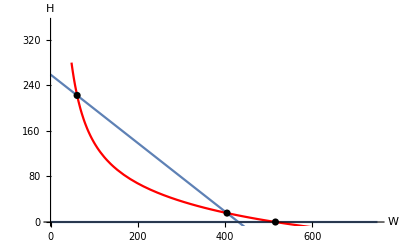

```mathematica
ph1=Plot[hnull1,{W,0,750}];
ph2=Plot[hnull2,{W,0,750}];
pw1=Plot[wnull1,{W,0,750},PlotStyle->Red];
pw2=Plot[wnull2,{W,0,750},PlotStyle->Red];
points=ListPlot[{fp2,fp3,fp4},PlotStyle->Black];
Show[ph1,ph2,pw1,pw2,points,PlotRange->{0,350},AxesLabel->{W,H}]
```

Stability Analysis

First fixed point: stable

```mathematica
j11=D[hdot[H,W],H]/.fp[[2]];
j12=D[hdot[H,W],W]/.fp[[2]];
j21=D[wdot[H,W],H]/.fp[[2]];
j22=D[wdot[H,W],W]/.fp[[2]];
J={{j11,j12},{j21,j22}};
Eigenvectors[J];
Eigenvalues[J]
```

{-1.53237,-0.497522}

Second fixed point: saddle

```mathematica
j11=D[hdot[H,W],H]/.fp[[4]];
j12=D[hdot[H,W],W]/.fp[[4]];
j21=D[wdot[H,W],H]/.fp[[4]];
j22=D[wdot[H,W],W]/.fp[[4]];
J={{j11,j12},{j21,j22}}
Eigenvectors[J]
Eigenvalues[J]
```

{{-0.0701114,0.},{-0.998278,-0.382467}}

{{0.,1.},{0.298618,-0.954373}}

{-0.382467,-0.0701114}

```mathematica
Inverse[J]
```

{{7.84948,-0.53845},{-47.6127,0.897417}}

Third fixed point: stable

{-0.382467,-0.140111}

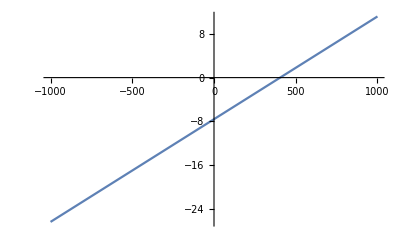

```mathematica
j11=D[hdot[H,W],H]/.fp[[4]];
j12=D[hdot[H,W],W]/.fp[[4]];
j21=D[wdot[H,W],H]/.fp[[4]];
j22=D[wdot[H,W],W]/.fp[[4]];
J={{j11,j12},{j21,j22}};
Eigenvectors[J];
Eigenvalues[J]
```